FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

|H(ω)| = (20 Log[30])/Log[10]+(20 Log[Abs[1+(ⅈ ω)/10]])/Log[10]-(20 Log[Abs[1+(ⅈ ω)/5]])/Log[10]-(20 Log[Abs[ω]])/Log[10]

|ϕ(ω)| = -90+(180 ArcTan[ω/10])/π-(180 ArcTan[ω/5])/π

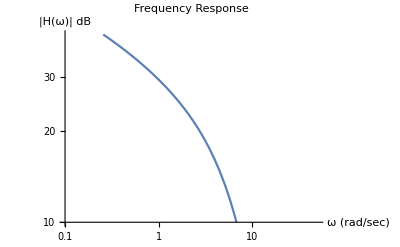

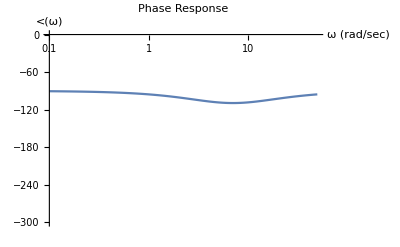

```mathematica
(*Start of Program*)
Clear["Global`*"]
K=Input["Enter The Value Of Gain"];

n = Input["Enter The Number Of Nonorigin Poles"];
listOfPoles =Table[Input["Enter The Value Of A Pole"],n];

z = Input["Enter The Number Of Nonorigin Zeros"];
listOfZeros = Table[Input["Enter The Value Of A Zero"],z];

op = Input["Enter The Number Of Origin Poles"];
oz = Input["Enter The Number Of Origin Zeros"];



listOfTerms1=20*Log[10,Abs[(1+(ⅉ ω)/#)&[listOfZeros]]];
listOfTerms2=20*Log[10,Abs[(1+(ⅉ ω)/#)&[listOfPoles]]];

listOfPhases1=(1/#)&[listOfZeros];
listOfPhases2=(1/#)&[listOfPoles];

largestPole=Max[listOfPoles];

(*H=Times@@listOfTerms*)

H[ω_]:=K*Times@@((1*(1+(ⅉ*ω)/#1)*(ⅉ*ω)^oz)/((1+(ⅉ*ω)/#2)*(ⅉ*ω)^op))&[listOfZeros,listOfPoles];(*This makes the function ∏_(i=1)^n 1/(1+ⅉω/Subscript[p, i])*)
	
StringForm["H(ⅉω)= ``",H[ω]];
peakMag = FindMaximum[Abs[H[ω]],ω][[1]];

dB[ω_]:=20*Log[10,K]+(Plus@@+listOfTerms1)+(Plus@@-listOfTerms2)+oz*20*Log[10,Abs[ⅉ*ω]]-op*20*Log[10,Abs[ⅉ*ω]]
ϕ[ω_]:=Arg[K]+(Plus@@+(180/π*ArcTan[ω*#]&[listOfPhases1]))+(Plus@@-(180/π*ArcTan[ω*#]&[listOfPhases2]))+ 90*oz - 90*op

StringForm["|H(ω)| = ``", dB[ω]]
StringForm["|ϕ(ω)| = ``", ϕ[ω]]
LogLogPlot[dB[ω],{ω,0.1,10*largestPole},PlotRange->{{0.1,10*largestPole},{10,28*Log[10,K]}},PlotLabel->"Frequency Response", AxesLabel->{"ω (rad/sec)","|H(ω)| dB"}]
LogLinearPlot[ϕ[ω], {ω,0.1,10*largestPole},PlotRange->{{0.1,10*largestPole},{-300,0}},PlotLabel->"Phase Response", AxesLabel->{"ω (rad/sec)","<(ω)"}]
```

```mathematica
2
```